```mathematica
<<UNET`
```

## Generated Data

### Examples of Test Data

```mathematica
{data,label}=CreateImage1[];
Flatten@{MakeChannelImage[data],Image[label]}
```

{-Graphics-,-Graphics-}

```mathematica
{data,label}=CreateImage2[];
Flatten@{MakeChannelImage[data],MakeClassImage[label]}
```

{-Graphics-,-Graphics-}

```mathematica
{data,label}=CreateImage3[];
Flatten@{MakeChannelImage[data],MakeClassImage[label,{1,4}]}
```

{-Graphics-,-Graphics-}

```mathematica
{data,label}=CreateImage4[];
Flatten@{MakeChannelImage[data],MakeClassImage[label,{1,4}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Test Cases 1: 1 channel - 1 classes

```mathematica
(*make test data*)
{data1,label1}=MakeTestImages[50,1];
```

```mathematica
(*split the data*)
{train1,valid1,testData1,testLabel1}=SplitTrainData[data1,label1];
```

Nuber of Samples in each set: {35,10,5}

```mathematica
(*visualize the test data*)
ShowChannelClassData[testData1,testLabel1, NumberRowItems->3,MakeDifferenceImage->False,StepSize->1]
```

-Graphics- | -Graphics- | -Graphics-

channels: 1 - classes: 1 - Dimensions :{128,128}

DICE per class: {1→0.978}

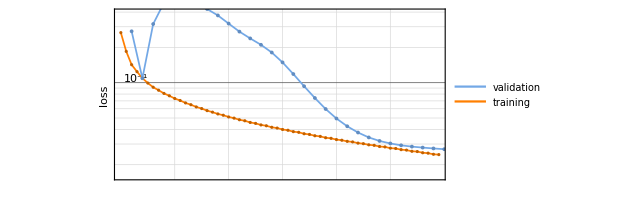

```mathematica
(*train the net*)
{{net1,trained1,netTrained1},{plots1,result1,iou1}}=TrainUNET[train1,valid1,{testData1,testLabel1},
TargetDevice->"GPU",MaxTrainingRounds->30,NetParameters->8];
plots1
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData,netTrained]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData1,testLabel1,result1, NumberRowItems->3,MakeDifferenceImage->False,StepSize->1]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
(*visualize the test data with diff image*)
ShowChannelClassData[testData1,testLabel1,result1, NumberRowItems->3,MakeDifferenceImage->True,StepSize->1]
```

-Graphics- | -Graphics- | -Graphics-

### Test Case 2: 1 channel - 2 classes

```mathematica
(*make test data*)
{data2,label2}=MakeTestImages[75,2];
```

```mathematica
(*split the data*)
{train2,valid2,testData2,testLabel2}=SplitTrainData[data2,label2];
```

Nuber of Samples in each set: {52,15,8}

channels: 1 - classes: 2 - Dimensions :{128,128}

DICE per class: {1→0.996,2→0.982}

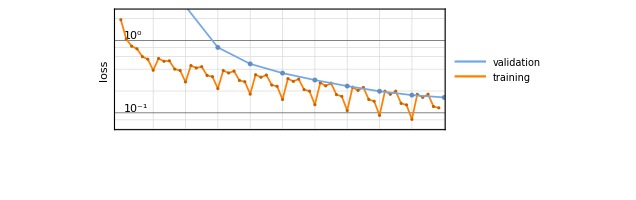
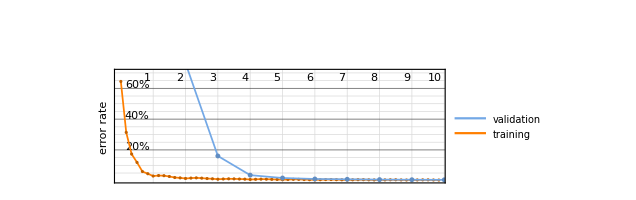

```mathematica
(*train the net*)
{{net2,trained2,netTrained2},{plots2,result2,iou2}}=TrainUNET[train2,valid2,{testData2,testLabel2},
TargetDevice->"GPU",MaxTrainingRounds->10,NetParameters->16];
plots2
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData2,netTrained2]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData2, testLabel2,result2, NumberRowItems->3,MakeDifferenceImage->False,StepSize->1]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

### Test Case 3: 1 channel - 4 classes

```mathematica
(*make test data*)
{data3,label3}=MakeTestImages[75,3];
```

```mathematica
(*data augmentation, increase the data by flipping and rotating*)
(*visualize the flips and rotations*)
data3R=RotateFlip[data3[[1;;2]]];
label3R=RotateFlip[label3[[1;;2]]];
ShowChannelClassData[data3R,label3R, NumberRowItems->4,MakeDifferenceImage->False,StepSize->1,ImageSize->100]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*split the data*)
{train3,valid3,testData3,testLabel3}=SplitTrainData[data3,label3,AugmentTrainData->True];
```

Nuber of Samples in each set: {52,15,8}

Nuber of Samples in each set afeter augmentation: {416,120,8}

channels: 1 - classes: 4 - Dimensions :{128,128}

DICE per class: {1→1.,2→0.928,3→0.961,4→0.997}

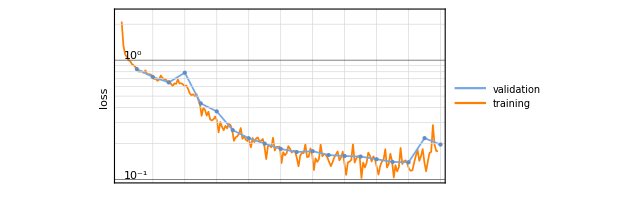
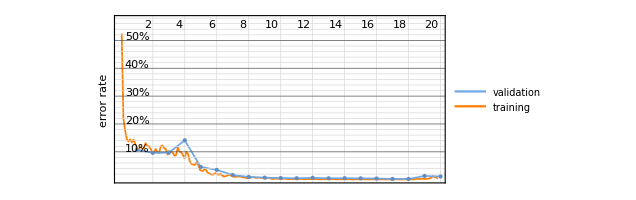

```mathematica
(*train the net*)
{{net3,trained3,netTrained3},{plots3,result3,iou3}}=TrainUNET[train3,valid3,{testData3,testLabel3},
TargetDevice->"GPU",MaxTrainingRounds->20,NetParameters->16];
plots3
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData3,netTrained3]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData3, testLabel3, result3, NumberRowItems->2,MakeDifferenceImage->False,StepSize->1]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

### Test Case 4 : 3 channels - 4 classes

```mathematica
(*make test data*)
{data4,label4}=MakeTestImages[100,4];
```

```mathematica
(*split the data*)
{train4,valid4,testData4,testLabel4}=SplitTrainData[data4,label4];
```

Nuber of Samples in each set: {70,20,10}

channels: 3 - classes: 4 - Dimensions :{128,128}

DICE per class: {1→0.999,2→0.992,3→0.993,4→0.951}

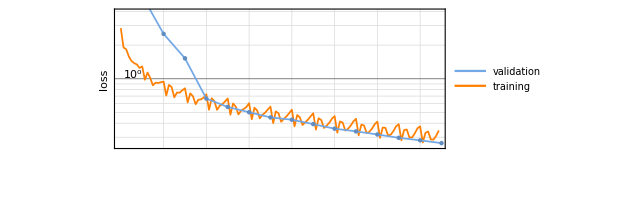
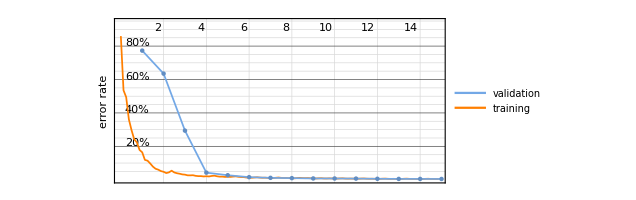

```mathematica
(*train the net*)
{{net4,trained4,netTrained4},{plots4,result4,iou4}}=TrainUNET[train4,valid4,{testData4,testLabel4},
TargetDevice->"GPU",MaxTrainingRounds->15,NetParameters->16];
plots4
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData4,netTrained4]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData4, testLabel4, result4, NumberRowItems->2,MakeDifferenceImage->True,StepSize->1,ImageSize->650]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

### Test Case 5 - same as 4 with animation

```mathematica
{data5,label5}=MakeTestImages[100,4];
```

```mathematica
{train5,valid5,testData5,testLabel5}=SplitTrainData[data5,label5];
```

Nuber of Samples in each set: {70,20,10}

```mathematica
(*choose a nice image*)
MakeChannelImage/@testData5
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
im=9;nchan=Max[testLabel5];solutions={};
imChan=First@MakeChannelImage[testData[[im,{1}]]];
(*The monitoring function*)
monitor=AppendTo[solutions,ClassDecoder[NetExtract[#Net,"net"][testData[[im]],TargetDevice->"GPU"],nchan]]&;

(*train the net with monitor function*)
{{net,trained,netTrained},{plots,result,iou}}=TrainUNET[train,valid,{testData,testLabel}, TargetDevice->"GPU",MaxTrainingRounds->10,NetParameters->16,
TrainingProgressFunction->{monitor,"Interval"->Quantity[2,"Batches"]}];
```

channels: 1 - classes: 4 - Dimensions :{128,128}

DICE per class: {1→0.999,2→0.948,3→0.966,4→0.991}

```mathematica
(*make the animation images*)
solIm=ColorReplace[MakeClassImage[#,{1,4}],ColorData["Rainbow"][0]]&/@solutions;
anim=Table[Show[ImageCompose[imChan,{sol,.5}],ImageSize->500],{sol,solIm}];
```

```mathematica
(*play the animatin*)
Animate[im,{im,anim}]
```